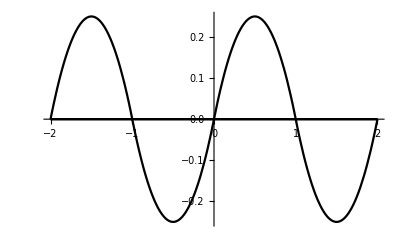

```mathematica
Plot[Table[Piecewise[{{(x-2*n)(1+(x-2*n)),-1+2*n<=x<2*n},{(x-2*n)(1-(x-2*n)),2*n≤x<1+2*n}}],{n,{-1,0,1}}],{x,-2,2},AxesStyle->Arrowheads[0.04],PlotStyle->Black]
```

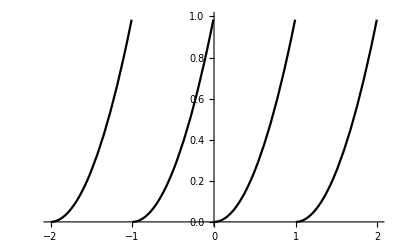

```mathematica
{m1,m2,m3,m4}=Graphics/@{{EdgeForm[Thick],White,Disk[{0,0},1]},Disk[{0,0},1],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]};
Show[Plot[Piecewise[{{(x+2)^2,-2≤x<-1},{(x+1)^2,-1≤x<0},{(x)^2,0≤x<1},{(x-1)^2,1≤x<2}}],{x,-2,2},AxesStyle->Arrowheads[0.04],PlotStyle->Black],ListPlot[{{-1,1},{0,1},{1,1},{2,1}},AxesStyle->Arrowheads[0.04],PlotStyle->Black,PlotMarkers->{m1,0.04}]]
```

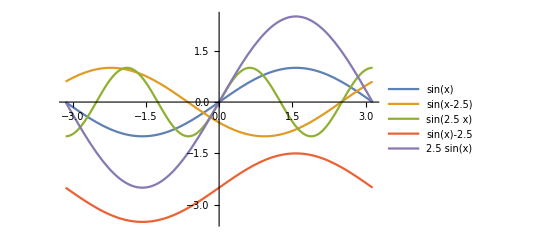

```mathematica
Plot[{Sin[x],Sin[x-2.5],Sin[2.5*x],Sin[x]-2.5,2.5*Sin[x]},{x,-Pi,Pi},AxesStyle->Arrowheads[0.04],PlotLegends->"Expressions"]
```

```mathematica
Solve[-Sqrt[n*Pi]+n==2*k,n]
```

{{n→1/2 (4 k+π-√π √(8 k+π))},{n→1/2 (4 k+π+√π √(8 k+π))}}

```mathematica
Solve[-Sqrt[n*Pi]+n==2*k+1-Pi/2,n]
```

{{n→1/2 (2+4 k-√π √(8 k+(64 π-16 π^2)/(16 π)))},{n→1/2 (2+4 k+√π √(8 k+(64 π-16 π^2)/(16 π)))}}